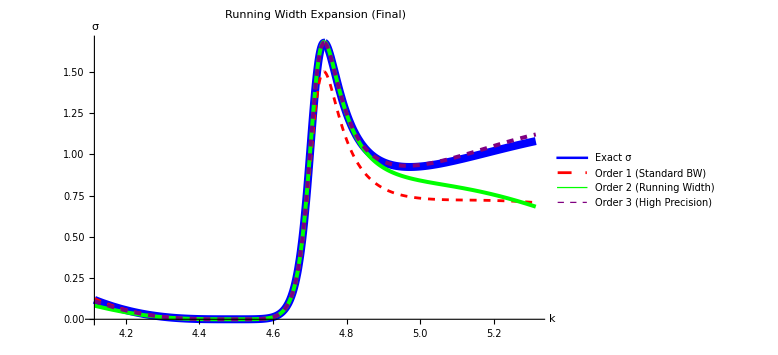

```mathematica
ClearAll["Global`*"]

(*1. Parameters*)
l=1;
μ=1;
a=1;
λ=20;

(*2. Exact Functions*)
Num[k_]:=SphericalBesselJ[l,k*a]^2;
Denom[k_]:=1-I*k*λ*a^2*SphericalBesselJ[l,k*a]*SphericalHankelH1[l,k*a];
UnitaryLimit[k_]:=(4*Pi/k^2)*(2*l+1);

(*Exact Sigma*)
ExactShape[k_]:=Abs[(-(I*k*λ*a^2)*Num[k])/Denom[k]]^2;
SigmaExact[k_]:=UnitaryLimit[k]*ExactShape[k];

(*3. Find Pole*)
searchGuess=4.7-0.1 I;
root=FindRoot[Denom[k]==0,{k,searchGuess}];
kres=k/. root;

(*4. RUNNING WIDTH EXPANSION (FIXED)*)

(*Use a dedicated Global symbol'kGen' for the series generation*)
(*This prevents the z$xxxx variable leakage*)
GetDenomPoly[n_]:=GetDenomPoly[n]=Normal[Series[Denom[kGen],{kGen,kres,n}]];

SigmaRunning[kVal_,n_]:=Module[{DApprox,NumVal,PolySymbolic},(*1. Retrieve the memoized polynomial (in terms of kGen)*)PolySymbolic=GetDenomPoly[n];
(*2. Replace kGen with the actual number kVal*)(*This is safe because kGen is global and unique*)DApprox=PolySymbolic/. kGen->kVal;
(*3. Calculate Sigma*)NumVal=-(I*kVal*λ*a^2)*Num[kVal];
UnitaryLimit[kVal]*Abs[NumVal/DApprox]^2];

(*5. Visualization*)
Plot[{SigmaExact[k],SigmaRunning[k,1],(*Order 1=Standard BW*)SigmaRunning[k,2],(*Order 2=Corrects the Shift*)SigmaRunning[k,3]    (*Order 3=Precision Fit*)},{k,Re[kres]-0.6,Re[kres]+0.6},PlotStyle->{{Blue,Thickness[0.01]},{Red,Dashed},{Green,Thickness[0.005]},{Purple,Dashed,Thickness[0.005]}},PlotLegends->{"Exact σ","Order 1 (Standard BW)","Order 2 (Running Width)","Order 3 (High Precision)"},AxesLabel->{"k","σ"},PlotLabel->"Running Width Expansion (Final)",PlotRange->All,ImageSize->Large]
```